```mathematica
ClearAll["Global`*"]
(* set your home directory *)
SetDirectory[NotebookDirectory[]];
```

# CATS’ PDEs Logo

## MeshRegion[]

#### Head

```mathematica
headNodes=Table[{Cos[i π/4+π/8],Sin[i π/4+π/8]},{i,1,8}];
```

#### Ears

```mathematica
rightEar=(headNodes[[1]]+headNodes[[8]])/2+RotationMatrix[270 Degree].(Sin@(π/3)(headNodes[[1]]-headNodes[[8]]));
leftEar=(headNodes[[2]]+headNodes[[3]])/2+RotationMatrix[270 Degree].(Sin@(π/3)(headNodes[[3]]-headNodes[[2]]));
earsNodes={rightEar,leftEar};
```

#### Nose

```mathematica
ℓ=Norm[headNodes[[2]]-headNodes[[1]]];
noseNodes={
{0,0},
{0,-ℓ/4},
{ℓ/4,-ℓ/3},{ℓ/2,-ℓ/4},
{-ℓ/4,-ℓ/3},{-ℓ/2,-ℓ/4}
};
```

#### Assembled Region

```mathematica
nodes=Join[headNodes,earsNodes,noseNodes];
ribs=Line/@{
{1,2},{2,10},{10,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,1},(* head + ears ribs *)
{11,12},{12,13},{13,14},{12,15},{15,16}
};
```

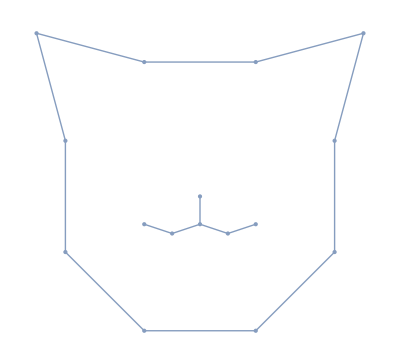

```mathematica
ℋ=MeshRegion[nodes,ribs]
```

```mathematica
𝒦=ToElementMesh[ℋ,"MaxCellMeasure"-> ℓ/4,"MeshOrder"->1];
nodes=𝒦[[1]];
triangles=𝒦[[2,1,1]];
Export["nodes.dat",Prepend[nodes,Length@nodes]];
Export["triangles.dat",Prepend[triangles,Length@triangles]];
```

```mathematica
ℛ=MeshRegion@𝒦;
HighlightMesh[ℛ,Labeled[0,"Index"]]
```

-Graphics-